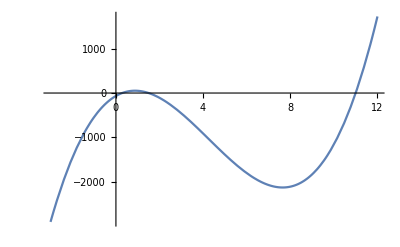

```mathematica
f[x_] := 14 x^3-179 x^2+281x - 66
Plot[f[x],{x,-3,12}, AxesOrigin->{0,0}]
```

```mathematica
Solve[f[x]==0]
```

{{x→2/7},{x→3/2},{x→11}}

```mathematica
a=0;
b=1;
e=0.001;
max=1000;
i=0;
While[i<max,
f1=f[a];
f2=f[b];
c=a-f1*(b-a)/(f2-f1);
If[Abs[f[c]]<e,Break[]];
If[f1*f[c]<0,b=c,a=c];
If[i==0,L1=a;R1=b];
If[i==1,L2=a;R2=b];
i++;
]
N[c,3]
```

0.286

```mathematica
N[i]
```

8.

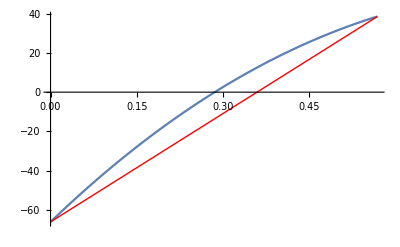

```mathematica
Plot[f[x],{x,L1,R1},
Epilog->{
{Red,Line[{{L1,f[L1]},{R1,f[R1]}}]}
}
]
```

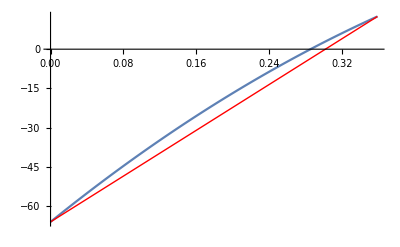

```mathematica
Plot[f[x],{x,L2,R2},
Epilog->{
{Red,Line[{{L2,f[L2]},{R2,f[R2]}}]}
}
]
```